```mathematica
SetDirectory[NotebookDirectory[]];
dat=Partition[Import["detections.csv"],4];
```

```mathematica
Degrees=Pi/180.0;
EqToEc[{raraw_,decraw_}]:=(
ra = Mod[raraw,360];
dec=Mod[decraw,360];
b=23.43928;
a=ArcCos[Cos[b Degrees]*Sin[dec Degrees]-Sin[b Degrees]*Cos[dec Degrees]*Sin[ra Degrees]]/Degrees;
CC=ArcCos[(Sin[dec Degrees]-Cos[a Degrees]Cos[b Degrees])/(Sin[a  Degrees]Sin[b Degrees])]/Degrees;
lon=90+If[90<ra<270,+1,-1]*CC;
lat = 90-a;
{lon,lat})
dat[[All,All,4;;5]]=Map[EqToEc,dat[[All,All,4;;5]],{2}];
```

```mathematica
PosVel[entry_]:=(dt=entry[[4,1]]-entry[[1,1]];{entry[[1,4]],entry[[1,5]],(entry[[4,4]]-entry[[1,4]])/dt,(entry[[4,5]]-entry[[1,5]])/dt})
mainBelt=PosVel/@Select[dat,#[[1,-1]]==0&];
neos=PosVel/@Select[dat,#[[1,-1]]==1&];
```

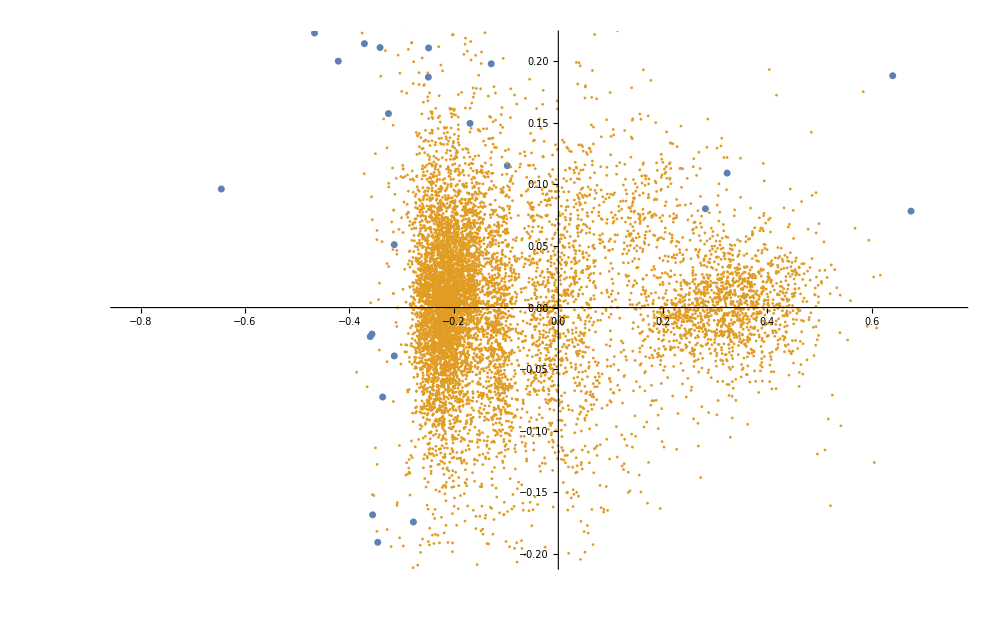

```mathematica
ListPlot[{neos[[All,{3,4}]],mainBelt[[All,{3,4}]]},PlotStyle->{Directive[AbsolutePointSize[5]],Directive[AbsolutePointSize[2]]}]
```